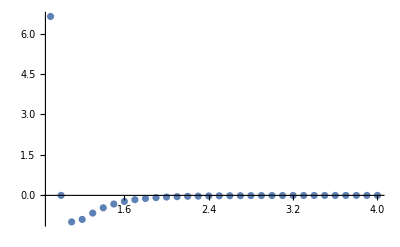

```mathematica
LJEnergy[r_]=4.0(1/r^12-1/r^6);
NoiseStrength=0.0000001;
(*DataLJ=Table[{r,LJEnergy[r]+NoiseStrength * RandomReal[{-Abs[LJEnergy[r]],Abs[LJEnergy[r]]}]},{r,0.9,4,0.05}];*)
DataLJ=Table[{r,LJEnergy[r]+NoiseStrength * RandomReal[{-1,1}]},{r,0.9,4.0,0.1}];
DataLJN=Round[Table[{r,LJEnergy[r]},{r,0.9,4.0,0.1}],NoiseStrength];
ListPlot[DataLJN,PlotRange->All]
```

```mathematica
DataLJ
DataLJN
```

{{0.9,6.63612},{1.,-8.80983×10^-8},{1.1,-0.983372},{1.2,-0.890965},{1.3,-0.657017},{1.4,-0.460687},{1.5,-0.320337},{1.6,-0.224208},{1.7,-0.158851},{1.8,-0.114147},{1.9,-0.0832162},{2.,-0.0615235},{2.1,-0.0460947},{2.2,-0.0349684},{2.3,-0.0268379},{2.4,-0.0208216},{2.5,-0.0163169},{2.6,-0.0129065},{2.7,-0.0102981},{2.8,-0.00828337},{2.9,-0.0067133},{3.,-0.00547935},{3.1,-0.004502},{3.2,-0.00372188},{3.3,-0.00309489},{3.4,-0.00258759},{3.5,-0.00217473},{3.6,-0.00183677},{3.7,-0.00155849},{3.8,-0.001328},{3.9,-0.00113651},{4.,-0.000976372}}

{{0.9,6.63612},{1.,0.},{1.1,-0.983372},{1.2,-0.890965},{1.3,-0.657017},{1.4,-0.460687},{1.5,-0.320337},{1.6,-0.224208},{1.7,-0.158851},{1.8,-0.114147},{1.9,-0.0832161},{2.,-0.0615234},{2.1,-0.0460947},{2.2,-0.0349685},{2.3,-0.0268379},{2.4,-0.0208216},{2.5,-0.0163169},{2.6,-0.0129066},{2.7,-0.010298},{2.8,-0.0082834},{2.9,-0.0067134},{3.,-0.0054794},{3.1,-0.0045019},{3.2,-0.0037218},{3.3,-0.0030949},{3.4,-0.0025876},{3.5,-0.0021748},{3.6,-0.0018367},{3.7,-0.0015584},{3.8,-0.001328},{3.9,-0.0011364},{4.,-0.0009763}}

```mathematica
ModelE=Table[r^-n,{n,1,15}];
LJFit=LinearModelFit[DataLJN,ModelE,r,IncludeConstantBasis->False];
```

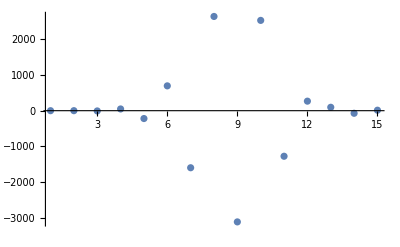

{-0.0240097,0.612791,-7.043,48.2289,-219.296,693.937,-1594.65,2633.41,-3107.96,2523.57,-1273.46,266.353,95.1984,-72.4919,13.6115}

{-4.,4.}

```mathematica
LJFitCorrect=LinearModelFit[DataLJN,{r^-6,r^-12},r,IncludeConstantBasis->False];
Plot1=ListPlot[LJFit["BestFitParameters"],PlotRange->All]
Round[LJFit["BestFitParameters"],NoiseStrength]
Round[LJFitCorrect["BestFitParameters"],NoiseStrength]
```

```mathematica
{-3.032896153379854,86.13362585261522,-1115.0532698218144,8722.08985915515,-46061.01993954486,173753.2485511304,-482966.4366780219,1.0051169239703263*^6,-1.5743191070542305*^6,1.847465435997105*^6,-1.5994907851805328*^6,991072.8844041899,-415603.4846312031,105619.26386407042,-12277.060623323787}
```

{-4.,4.}

```mathematica
Export["LJ-OLS.eps",Plot1];
```

```mathematica
Map[Function[x,x^2],ListResiduals]
```

{1.36142×10^-22,2.90777×10^-21,2.85542×10^-19,3.21186×10^-17,1.15833×10^-15,1.31802×10^-14,3.70063×10^-14,1.48541×10^-15,1.05587×10^-13,1.67715×10^-14,5.94197×10^-13,4.44564×10^-13,4.06059×10^-13,2.79069×10^-13,3.83224×10^-13,9.97433×10^-14,2.8929×10^-14,6.41349×10^-14,1.36998×10^-13,4.52893×10^-14,3.49927×10^-17,1.58825×10^-14,1.94339×10^-15,6.90048×10^-14,2.17809×10^-13,3.82073×10^-13,1.62966×10^-12,5.91901×10^-16,6.50629×10^-13,2.48338×10^-13,9.32348×10^-14,1.64698×10^-14}

{1.1668×10^-11,-5.39238×10^-11,-5.34361×10^-10,5.66733×10^-9,-3.40342×10^-8,1.14805×10^-7,-1.9237×10^-7,3.8541×10^-8,3.24941×10^-7,-1.29505×10^-7,-7.70842×10^-7,6.66756×10^-7,6.37228×10^-7,-5.2827×10^-7,-6.19051×10^-7,3.15822×10^-7,1.70085×10^-7,2.53249×10^-7,-3.70132×10^-7,2.12813×10^-7,-5.91547×10^-9,-1.26026×10^-7,4.40839×10^-8,2.62688×10^-7,-4.667×10^-7,-6.1812×10^-7,1.27658×10^-6,2.4329×10^-8,-8.06615×10^-7,4.98335×10^-7,-3.05344×10^-7,1.28335×10^-7}

4.32402×10^-7

1.27658×10^-6

6.01289×10^-7

1.02637×10^-6

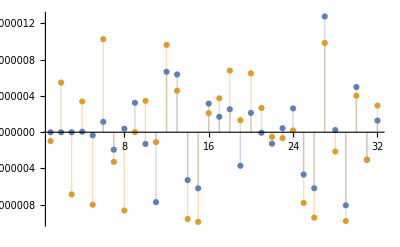

```mathematica
ListResiduals=LJFit["FitResiduals"]
RMSE1=Sqrt[Total[Map[Function[x,x^2],ListResiduals]]/Length[ListResiduals]]
MaxE1=Max[Abs[ListResiduals]]
ListResidualsC=LJFitCorrect["FitResiduals"];
RMSEC=Sqrt[Total[Map[Function[x,x^2],ListResidualsC]]/Length[ListResidualsC]]
MaxEC=Max[Abs[ListResidualsC]]
ListPlot[{ListResiduals,ListResidualsC}, Filling->Axis,PlotRange->All]
```

```mathematica
LJFit["BestFitParameters"]
LJFit["Function"]
```

{0.0075223,-17.671,250.235,-1647.8,6492.49,-16792.4,29560.7,-35778.2,29352.6,-15610.9,4863.4,-672.39}

0.0075223-672.39/#1^13+4863.4/#1^12-15610.9/#1^11+29352.6/#1^10-35778.2/#1^9+29560.7/#1^8-16792.4/#1^7+6492.49/#1^6-1647.8/#1^5+250.235/#1^4-17.671/#1^3&